Plot the polar plot of the solution for laser melts

```mathematica
F[r_,R_]:= ((R^2+1)/(R^2-1)Log[R]-1)^-1 (-r/2+(R^2+1)/(R^2-1) r Log[r] + R^2/(2 r (R^2-1))-r^3/(2 (R^2-1)))
```

```mathematica
ρ = 4450; (*density in kg/m^3 *)
cp = 546;(* specific heat in J/kg K *)
k = 6 ; (*conductivity W/m K *)
U = 0.05; (* scanning speed in m/s *)
a=0.0005;  (* characteristic length in m *)
```

```mathematica
q=ρ cp U a /k; (* Peclet number *)
u1=0.9; R=(1/q)^(u1/(1+u1))
```

0.33403

I am not sure that here we have Sin[θ] maybe it is Cos[θ].

```mathematica
ϕ[r_,θ_]:= F[r,R]*Sin[θ];
```

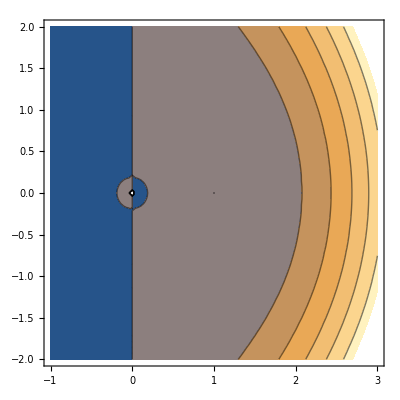

```mathematica
ContourPlot[ϕ[Sqrt[x^2+y^2],ArcTan[y,x]], {x,-1,3},{y,-2,2}]
```

This calculates the velocities in  x and y direction for the melt pool when conduction dominates the problem.

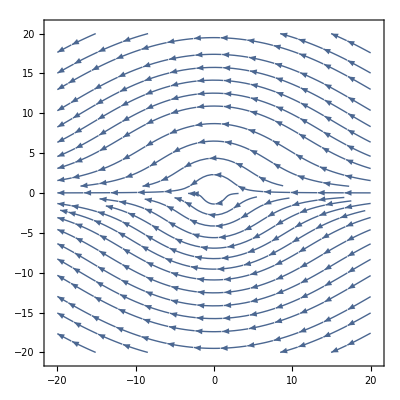

```mathematica
vx[x_,y_]:=Evaluate[-D[TransformedField["Polar"->"Cartesian", ϕ[r,θ],{r,θ}->{x,y}],y]];vy[x_,y_]:=Evaluate[D[TransformedField["Polar"->"Cartesian", ϕ[r,θ],{r,θ}->{x,y}],x]];

StreamPlot[{vx[x,y],vy[x,y]},
{x,-20,20},{y,-20,20}, AspectRatio->True]
```

Temperature in the molten region is given:

```mathematica
u[r_]:=u1-(u1 Log[r])/R;
```

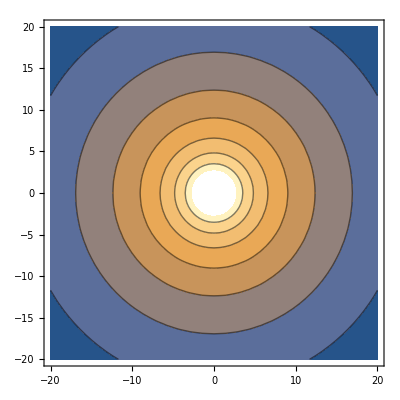

```mathematica
ContourPlot[u[Sqrt[x^2+y^2]], {x,-20,20},{y,-20,20}]
```

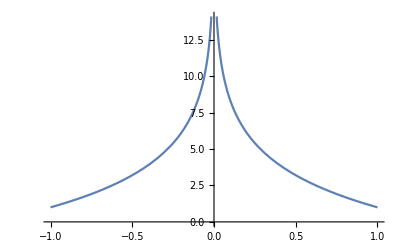

```mathematica
Plot[u[Sqrt[x^2]], {x,-1,1}]
```